```mathematica
Docu2[g_,n_]:={Graph[g,GraphLayout->"PlanarEmbedding"],
Reverse[PadRight[CompleteBaseCoeff[ ChromaticPolynomial[g,x]],n]]}
```

```mathematica
compPoly[g_,n_]:=PadRight[CompleteBaseCoeff[ ChromaticPolynomial[g,x]],n,0]
```

```mathematica
DoIt[g_]:=Block[{found},
found=Table[
With[
{n=VertexCount[g]+1},
With[
{base=EdgeDelete[g,e]},
{Graph[base,GraphLayout->"PlanarEmbedding"],TableForm[{compPoly[base,n],compPoly[base,n]-compPoly[g,n],compPoly[base,n]-compPoly[EdgeContract[g,e],n]}, TableDepth->2],Graph[g,GraphLayout->"PlanarEmbedding",GraphHighlight->e],Graph[EdgeContract[g,e],GraphLayout->"PlanarEmbedding"]}
]
],{e,EdgeList[g]}
]
]
```

```mathematica
DoIt2[g_]:=Block[{found},
found=Table[
With[
{n=VertexCount[g]+1},
With[
{base=EdgeDelete[g,e]},
{compPoly[EdgeContract[g,e],n],

Row[{
TableForm[{
compPoly[base,n],
Graph[base,GraphLayout->"PlanarEmbedding"]}, TableDepth->1],
"   =   ",
TableForm[{
compPoly[g,n],
Graph[g,GraphLayout->"PlanarEmbedding",GraphHighlight->e]}, TableDepth->1
],
"   +   ",
TableForm[{
compPoly[EdgeContract[g,e],n],
Graph[EdgeContract[g,e],GraphLayout->"PlanarEmbedding"]}, TableDepth->1
]}
]
}
]
]
,{e,EdgeList[g]}
]
]
```

```mathematica
OneGraph[g_,n_]:=TableForm[{
compPoly[g,n],
ChromaticPolynomial[g,4],
Framed[Graph[g,GraphLayout->"PlanarEmbedding"]]}, TableDepth->1]
```

```mathematica
DoIt3[g_]:=Block[{found},
found=Table[
With[
{n=VertexCount[g]+1},
With[
{base=EdgeDelete[g,e]},
{compPoly[EdgeContract[g,e],n],

Row[{
OneGraph[base,n],
Style["   =   ", FontSize->24],
OneGraph[g,n],
Style["   +   ", FontSize->24],
OneGraph[EdgeContract[g,e],n]
}
]
}
]
]
,{e,EdgeList[g]}
]
]
```

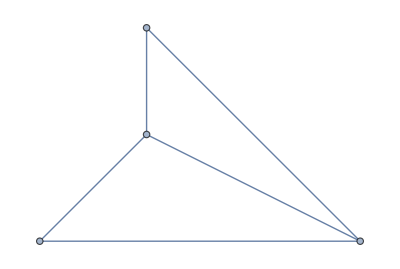
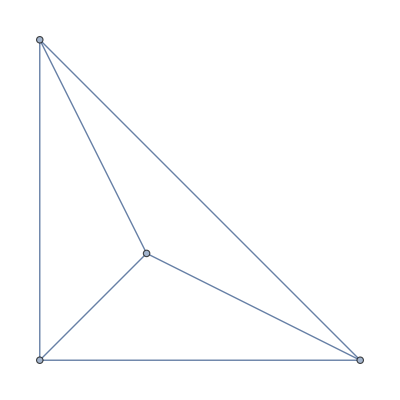
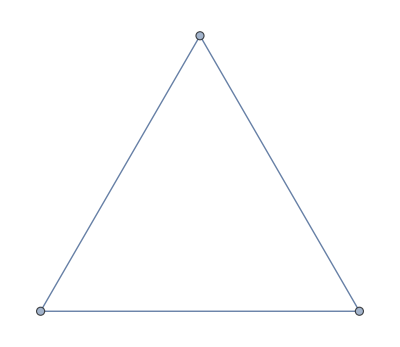
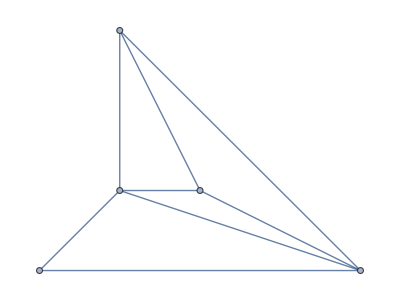
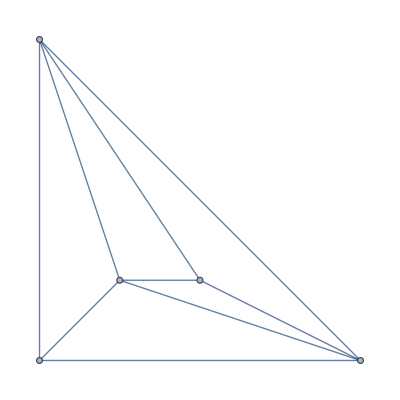
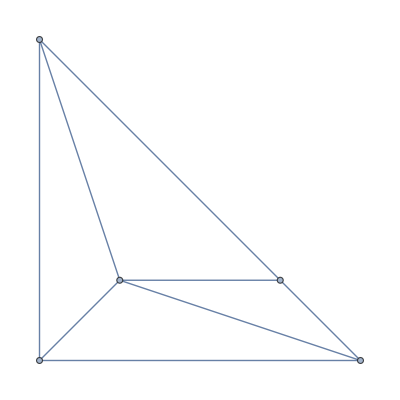
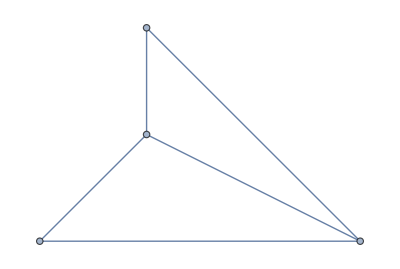
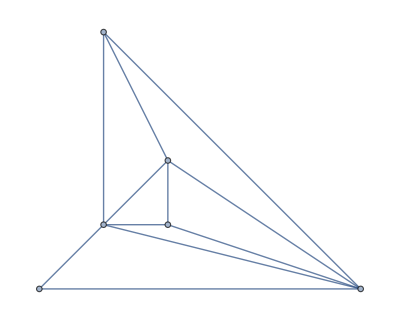
{0,0,0,1,1}
-Graphics-   =   {0,0,0,0,1}
-Graphics-   +   {0,0,0,1,0}
-Graphics-
{0,0,0,0,2,1}
-Graphics-   =   {0,0,0,0,1,1}
-Graphics-   +   {0,0,0,0,1,0}
-Graphics-
{0,0,0,1,2,1}
-Graphics-   =   {0,0,0,0,1,1}
-Graphics-   +   {0,0,0,1,1,0}
-Graphics-
{0,0,0,0,2,4,1}
-Graphics-   =   {0,0,0,0,1,3,1}
-Graphics-   +   {0,0,0,0,1,1,0}
-Graphics-
{0,0,0,0,3,4,1}
-Graphics-   =   {0,0,0,0,1,3,1}
-Graphics-   +   {0,0,0,0,2,1,0}
-Graphics-
{0,0,0,1,4,4,1}
-Graphics-   =   {0,0,0,0,1,3,1}
-Graphics-   +   {0,0,0,1,3,1,0}
-Graphics-
{0,0,0,0,2,10,7,1}
-Graphics-   =   {0,0,0,0,1,7,6,1}
-Graphics-   +   {0,0,0,0,1,3,1,0}
-Graphics-
{0,0,0,0,5,12,7,1}
-Graphics-   =   {0,0,0,0,1,7,6,1}
-Graphics-   +   {0,0,0,0,4,5,1,0}
-Graphics-
{0,0,0,0,3,11,7,1}
-Graphics-   =   {0,0,0,0,1,7,6,1}
-Graphics-   +   {0,0,0,0,2,4,1,0}
-Graphics-
{0,0,0,1,7,12,7,1}
-Graphics-   =   {0,0,0,0,4,9,6,1}
-Graphics-   +   {0,0,0,1,3,3,1,0}
-Graphics-
{0,0,0,1,8,13,7,1}
-Graphics-   =   {0,0,0,0,1,7,6,1}
-Graphics-   +   {0,0,0,1,7,6,1,0}
-Graphics-
{0,0,0,0,2,22,31,11,1}
-Graphics-   =   {0,0,0,0,1,15,25,10,1}
-Graphics-   +   {0,0,0,0,1,7,6,1,0}
-Graphics-
{0,0,0,0,5,29,33,11,1}
-Graphics-   =   {0,0,0,0,1,15,25,10,1}
-Graphics-   +   {0,0,0,0,4,14,8,1,0}
-Graphics-
{0,0,0,0,3,25,32,11,1}
-Graphics-   =   {0,0,0,0,1,15,25,10,1}
-Graphics-   +   {0,0,0,0,2,10,7,1,0}
-Graphics-
{0,0,0,0,10,35,34,11,1}
-Graphics-   =   {0,0,0,0,5,25,28,10,1}
-Graphics-   +   {0,0,0,0,5,10,6,1,0}
-Graphics-
{0,0,0,0,9,34,34,11,1}
-Graphics-   =   {0,0,0,0,5,25,28,10,1}
-Graphics-   +   {0,0,0,0,4,9,6,1,0}
-Graphics-
{0,0,0,1,12,37,35,11,1}
-Graphics-   =   {0,0,0,0,5,25,28,10,1}
-Graphics-   +   {0,0,0,1,7,12,7,1,0}
-Graphics-
{0,0,0,0,9,34,34,11,1}
-Graphics-   =   {0,0,0,0,1,15,25,10,1}
-Graphics-   +   {0,0,0,0,8,19,9,1,0}
-Graphics-

```mathematica
TableForm[
Map[Last[#]&,
DeleteDuplicates[
Flatten[
Table[
DoIt2[ReadGrof[k]],
{k,1,20}
],1],
#1[[1]]==#2[[1]]&]
]
]
```